## Европейский газовый рынок: сбор и визуализация данных, формирование балансовых таблиц по странам, оценка пропускных способностей трубопроводов

## Зелин И.А. , Смолянинов Д.А. СПбГЭУ, 2022

## 2. Доставка и хранение газа

```mathematica
-Graphics-       -Graphics--Graphics-
```

## 3. Балансовые таблицы: исходные данные (Eurostat)

123

nrg_cb_gasm - Supply, transformation and consumption of gas - monthly data

nrg_te_gasm - Exports of natural gas by partner country - monthly data

nrg_ti_gasm - Imports of natural gas by partner country - monthly data

## 4. Обработка данных по газовым потокам

техническая (форматная) составляющая

разделение на трубный и сжиженный

изменение маршрутов транспортировки

```mathematica
-Graphics-->-Graphics-
```

## 5. Балансовые таблицы: исходные данные (GIE)

12

## 6. Балансовые таблицы : составление

import | export
ugs_withdrawal | ugs_injection
production | consumption
lng_send_out | stat_mistake

приведение к схожим единицам измерения

корректная обработка отсутствия данных

построение предварительных таблиц в едином формате для слияния

выделение наиболее насыщенного данными временного промежутка

применение разных методик составления с целью минимизации ошибки

#### Пример предварительной таблицы ugs_injection

#### Альтернативная методика составления

import | export
--- | stock_changes
production | consumption
lng_send_out | stat_mistake

## 7. Балансовые таблицы

по данным Eurostat, AGSI, ALSI

с заменой данных AGSI на Eurostat

## 8. Балансовые таблицы: сравнение ошибок

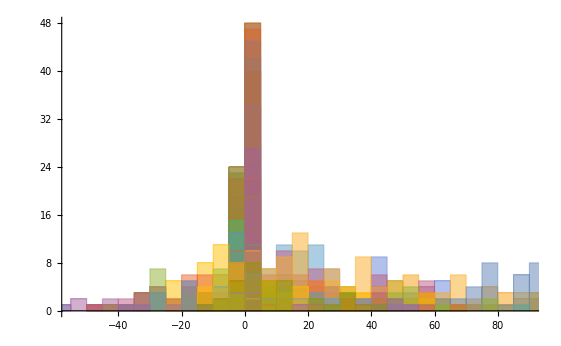
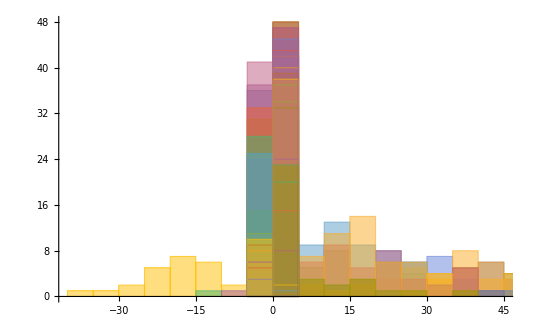

Медианы по модулю - 3.2 и ~0, средние по модулю - 19.1 и 10.8 соответственно

## 9. Оценка загруженности трубопроводной сети

На основе данных о пропускных способностях между странами от GIE и данных об импорте Eurostat

#### Часть 1: визуализация пропускных способностей

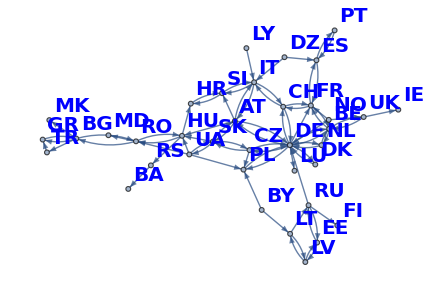
```mathematica
"   "-Graphics--Graphics--Graphics-
```

#### Часть 2: оценка заполненности и остаточные сети

выбор временных срезов: наиболее плотный (2018-2021)

```mathematica
12
```

и альтернативный: 2010-2013

```mathematica
12
```

## 10. Импорт и обработка данных из AGSI/ALSI

### Получение данных с помощью API

Парсинг данных.
Имортированные json-файлы с ссылками на данные переводим в ассоциацию. Перебираем все ссылки в этой ассоциации и скачиваем json-файл с данными по стране и компании. После чего экспортируем данные в json формате вида: страна_компания.json

-Graphics-

Структура получившегося JSON-файла,  полученного с помощью API GIE

Структура получившегося JSON-файла, скачанного для Austria, astora GmbH

## 11. Группировка данных и агрегирование

Агрегирование данных по месяцам. Получаем список fileNames всех имен файлов в директории исходных json-файлов с данными. Перебираем каждый файл, открываем его, конвертируем в Dataset, после чего группируем с помощью функции GroupBy, применяя функцию Mean, чтобы избежать ошибок, связанных с типом данных, конвертируем все в вещественные числа с помощью функции ToExpression. Далее экспортируем файлы вида: страна_компания.json в папку AGSI\ASLI_grouped

Структура получившегося JSON-файла, например данных Austria, astora GmbH

## 12. Составление единой таблицы данных.

Составление единой таблицы данных. Составлено две таблицы данных по AGSI\ALSI.
Получаем список fileNames всех имен файлов в директории исходных json-файлов с агрегированными по месяцам данными.
Проверяем, что файл содержит в себе данные, после чего конвертируем файл в список ассоциаций вида:

{Country - страна, Company - название_компании, Date -  Дата, gasInStorage - сколько газа в хранилищах (TWh), full - заполненость хранилища (%), injection - количество закачанного газа за месяц (GWh/m), withdrawal - количество выкачанного газа за месяц (GWh/m), workingGasVolume - объем рабочего газа (TWh), injectionCapacity - максимально возможный объем закачанного газа (GWh/m), withdrawalCapacity - максимально возможный объем выкачанного газа (GWh/m)} для данных AGSI

{Country - страна, Company - название_компании, Date -  Дата, lngInventory - количество сжиженного газа (m^3) , sendOut - отправленный газ за месяц (GWh/m) , dtmi - максимальный объем хранилища (m^3), dtrs - максимальный обхем отправки (GWh/m) } для данных ALSI

12

Пример датасета с данными из GIE.AGSI

## 13. Визуализация балансовой таблицы

### Сравнение различных данных балансовой таблицы

```mathematica
getComparativeByYear["NL", "2018"]
```

123

## 14. Визуализация того, за счет каких параметров происходит удовлетворение потребности в газе внутри страны

```mathematica
getMeetingDemandByYear["NL", "2018"]
```

123

## 15. Визуализация данных балансовой таблицы на карте

```mathematica
getGeoParamVisualisationByYear["2018"]
```

getGeoParamVisualisationByYear[2018]

## 16. Визуализация данных Eurostat

```mathematica
importData = getImportData[];
getGasFlowVisualisation[aggregate[getDataByYear[importData, "2018"], Mean]]
```

-Graphics-

## 17. Initialization

```mathematica
SetDirectory@NotebookDirectory[];
<<"WorkingWithData.wl"
<<"BalanceDataVisualisation.wl"
$Line = 0;
```

getGeoParamVisualisationByYear::shdw: Symbol getGeoParamVisualisationByYear appears in multiple contexts {BalanceDataVisualisation`,Global`}; definitions in context BalanceDataVisualisation` may shadow or be shadowed by other definitions.